```mathematica
Needs["Combinatorica`"];
linspace =Array[# &, 5, {-2,2}];
sq[a_,b_] = {Re[Sqrt[a+I*b]],Im[Sqrt[a+I*b]]};
grid = sq@@@CartesianProduct[linspace,linspace]
```

{{Re[√(-2-2 ⅈ)],Im[√(-2-2 ⅈ)]},{Re[√(-2-ⅈ)],Im[√(-2-ⅈ)]},{0,√2},{Re[√(-2+ⅈ)],Im[√(-2+ⅈ)]},{Re[√(-2+2 ⅈ)],Im[√(-2+2 ⅈ)]},{Re[√(-1-2 ⅈ)],Im[√(-1-2 ⅈ)]},{Re[√(-1-ⅈ)],Im[√(-1-ⅈ)]},{0,1},{Re[√(-1+ⅈ)],Im[√(-1+ⅈ)]},{Re[√(-1+2 ⅈ)],Im[√(-1+2 ⅈ)]},{1,-1},{1/(√2),-1/(√2)},{0,0},{1/(√2),1/(√2)},{1,1},{Re[√(1-2 ⅈ)],Im[√(1-2 ⅈ)]},{Re[√(1-ⅈ)],Im[√(1-ⅈ)]},{1,0},{Re[√(1+ⅈ)],Im[√(1+ⅈ)]},{Re[√(1+2 ⅈ)],Im[√(1+2 ⅈ)]},{Re[√(2-2 ⅈ)],Im[√(2-2 ⅈ)]},{Re[√(2-ⅈ)],Im[√(2-ⅈ)]},{√2,0},{Re[√(2+ⅈ)],Im[√(2+ⅈ)]},{Re[√(2+2 ⅈ)],Im[√(2+2 ⅈ)]}}

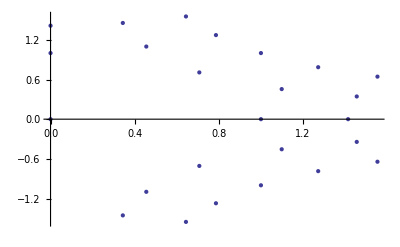

```mathematica
ListPlot[%82]
```

```mathematica
sq[{1,2}]
```

{Re[√(1+2 ⅈ)],Im[√(1+2 ⅈ)]}

```mathematica
CartesianProduct[linspace,I*linspace]
```

{{-2,-2 ⅈ},{-2,-ⅈ},{-2,0},{-2,ⅈ},{-2,2 ⅈ},{-1,-2 ⅈ},{-1,-ⅈ},{-1,0},{-1,ⅈ},{-1,2 ⅈ},{0,-2 ⅈ},{0,-ⅈ},{0,0},{0,ⅈ},{0,2 ⅈ},{1,-2 ⅈ},{1,-ⅈ},{1,0},{1,ⅈ},{1,2 ⅈ},{2,-2 ⅈ},{2,-ⅈ},{2,0},{2,ⅈ},{2,2 ⅈ}}

```mathematica
Sqrt@(Plus@@@Out[47])
```

{√(-2-2 ⅈ),√(-2-ⅈ),ⅈ √2,√(-2+ⅈ),√(-2+2 ⅈ),√(-1-2 ⅈ),√(-1-ⅈ),ⅈ,√(-1+ⅈ),√(-1+2 ⅈ),1-ⅈ,-(-1)^(3/4),0,(-1)^(1/4),1+ⅈ,√(1-2 ⅈ),√(1-ⅈ),1,√(1+ⅈ),√(1+2 ⅈ),√(2-2 ⅈ),√(2-ⅈ),√2,√(2+ⅈ),√(2+2 ⅈ)}

```mathematica
ViewRootSurface[n_Integer,resolution_Integer]:=ParametricPlot3D[{r*Cos[theta],r*Sin[theta], r^(1/n)*Cos[theta/n]},{r,0,.8},{theta,0,2Pi*n},PlotPoints->{resolution, resolution*n},Boxed->True, Axes->True,AspectRatio->1, ViewPoint->{-3,-3,0}]
```

```mathematica
Show[ViewRootSurface[1,20],ViewRootSurface[2,30]]
```

-Graphics3D-

```mathematica
ComplexToPolar[z_]/;z∈Complexes:=Abs[z] Exp[I Arg[z]]
```

```mathematica
ComplexToPolar[(-4)^(1/4)]
```

√2 ⅇ^((ⅈ π)/4)

```mathematica
f[z_]:=Sqrt[z];
```

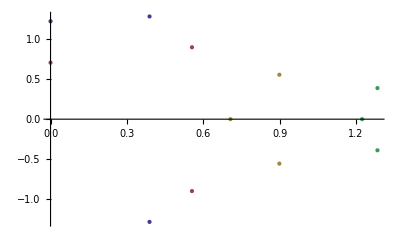

```mathematica
With[{maximumModulus=10},ListPlot[Table[{Re[f[x+I*y]],Im[f[x+I*y]]},{x,-1.5,1.5},{y,-1,1}]]]
```

```mathematica
Table[ⅇ^(i*t),{t,0,2Pi,Pi/64}]
```

{1,ⅇ^((i π)/64),ⅇ^((i π)/32),ⅇ^((3 i π)/64),ⅇ^((i π)/16),ⅇ^((5 i π)/64),ⅇ^((3 i π)/32),ⅇ^((7 i π)/64),ⅇ^((i π)/8),ⅇ^((9 i π)/64),ⅇ^((5 i π)/32),ⅇ^((11 i π)/64),ⅇ^((3 i π)/16),ⅇ^((13 i π)/64),ⅇ^((7 i π)/32),ⅇ^((15 i π)/64),ⅇ^((i π)/4),ⅇ^((17 i π)/64),ⅇ^((9 i π)/32),ⅇ^((19 i π)/64),ⅇ^((5 i π)/16),ⅇ^((21 i π)/64),ⅇ^((11 i π)/32),ⅇ^((23 i π)/64),ⅇ^((3 i π)/8),ⅇ^((25 i π)/64),ⅇ^((13 i π)/32),ⅇ^((27 i π)/64),ⅇ^((7 i π)/16),ⅇ^((29 i π)/64),ⅇ^((15 i π)/32),ⅇ^((31 i π)/64),ⅇ^((i π)/2),ⅇ^((33 i π)/64),ⅇ^((17 i π)/32),ⅇ^((35 i π)/64),ⅇ^((9 i π)/16),ⅇ^((37 i π)/64),ⅇ^((19 i π)/32),ⅇ^((39 i π)/64),ⅇ^((5 i π)/8),ⅇ^((41 i π)/64),ⅇ^((21 i π)/32),ⅇ^((43 i π)/64),ⅇ^((11 i π)/16),ⅇ^((45 i π)/64),ⅇ^((23 i π)/32),ⅇ^((47 i π)/64),ⅇ^((3 i π)/4),ⅇ^((49 i π)/64),ⅇ^((25 i π)/32),ⅇ^((51 i π)/64),ⅇ^((13 i π)/16),ⅇ^((53 i π)/64),ⅇ^((27 i π)/32),ⅇ^((55 i π)/64),ⅇ^((7 i π)/8),ⅇ^((57 i π)/64),ⅇ^((29 i π)/32),ⅇ^((59 i π)/64),ⅇ^((15 i π)/16),ⅇ^((61 i π)/64),ⅇ^((31 i π)/32),ⅇ^((63 i π)/64),ⅇ^(i π),ⅇ^((65 i π)/64),ⅇ^((33 i π)/32),ⅇ^((67 i π)/64),ⅇ^((17 i π)/16),ⅇ^((69 i π)/64),ⅇ^((35 i π)/32),ⅇ^((71 i π)/64),ⅇ^((9 i π)/8),ⅇ^((73 i π)/64),ⅇ^((37 i π)/32),ⅇ^((75 i π)/64),ⅇ^((19 i π)/16),ⅇ^((77 i π)/64),ⅇ^((39 i π)/32),ⅇ^((79 i π)/64),ⅇ^((5 i π)/4),ⅇ^((81 i π)/64),ⅇ^((41 i π)/32),ⅇ^((83 i π)/64),ⅇ^((21 i π)/16),ⅇ^((85 i π)/64),ⅇ^((43 i π)/32),ⅇ^((87 i π)/64),ⅇ^((11 i π)/8),ⅇ^((89 i π)/64),ⅇ^((45 i π)/32),ⅇ^((91 i π)/64),ⅇ^((23 i π)/16),ⅇ^((93 i π)/64),ⅇ^((47 i π)/32),ⅇ^((95 i π)/64),ⅇ^((3 i π)/2),ⅇ^((97 i π)/64),ⅇ^((49 i π)/32),ⅇ^((99 i π)/64),ⅇ^((25 i π)/16),ⅇ^((101 i π)/64),ⅇ^((51 i π)/32),ⅇ^((103 i π)/64),ⅇ^((13 i π)/8),ⅇ^((105 i π)/64),ⅇ^((53 i π)/32),ⅇ^((107 i π)/64),ⅇ^((27 i π)/16),ⅇ^((109 i π)/64),ⅇ^((55 i π)/32),ⅇ^((111 i π)/64),ⅇ^((7 i π)/4),ⅇ^((113 i π)/64),ⅇ^((57 i π)/32),ⅇ^((115 i π)/64),ⅇ^((29 i π)/16),ⅇ^((117 i π)/64),ⅇ^((59 i π)/32),ⅇ^((119 i π)/64),ⅇ^((15 i π)/8),ⅇ^((121 i π)/64),ⅇ^((61 i π)/32),ⅇ^((123 i π)/64),ⅇ^((31 i π)/16),ⅇ^((125 i π)/64),ⅇ^((63 i π)/32),ⅇ^((127 i π)/64),ⅇ^(2 i π)}

```mathematica
Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/64}]
```

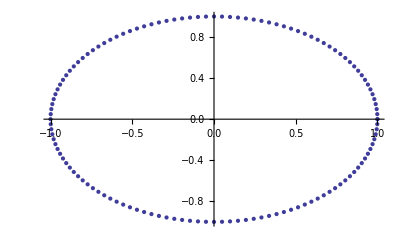

```mathematica
ListPlot[Table[{Cos[t],Sin[t]},{t,0,2Pi,Pi/64}]]
```

```mathematica
ComplexExpand
```